# Théorème de Stone - Weierstrass

## Exemple

### La fonction à approcher

```mathematica
F[x_] :=Exp[x]
```

### Le polynôme qui approche

```mathematica
Degré:=5
```

```mathematica
Poly=Normal[Series[F[x],{x,0,Degré}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

## Représentation

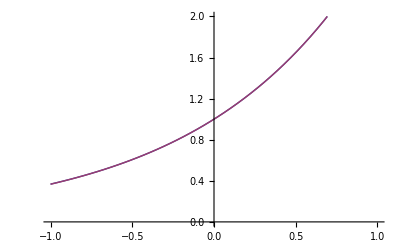

```mathematica
Plot[Evaluate[{F[x],Poly}],{x,-1,1},PlotRange->{0,2}]
```

```mathematica
Manipulate[Plot[Evaluate[{F[x],Normal[Series[F[x],{x,0,N}]]}],{x,-1,1},PlotRange->{0,2}],{N,1,Degré,1},ControlType->Setter]
```